## Initialization

```mathematica
<<FunctionApproximations`
```

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"functions","sin_cos_18_only1.wl"}]];Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"functions","sin_cos_18_not1.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"ieee754_floating_point.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"ieee754_floating_point_evaluation.wl"}]];
```

```mathematica
SetFloatingPointFormat[binary64];
SetRoundingMode[NearestTiesToEven];
```

```mathematica
On[Assert]
```

```mathematica
?IEEE754FloatingPoint`*
```

Syntax::sntxf: "?" cannot be followed by "IEEE754FloatingPoint`*".

Extra bits for argument reduction:

```mathematica
κ3=18
```

18

Characteristics of the floating-point model:

```mathematica
M=binary64[[1]]
```

53

```mathematica
𝔲[x_]:=FromRepresentation[Representation[x]+1]-x
```

```mathematica
Assert[𝔲[1]==2^(1-M)]
```

```mathematica
γ[n_]:=n 2^-M/(1-n 2^-M)
```

```mathematica
uInterval:=Interval[{-𝔲[1/2],𝔲[1/2]}]
```

## Approximation of π/2

This section verifies the error bounds for the approximations of π/2.

### Two - Term Approximation

```mathematica
κ1;κ′1;C1;δC1;
```

```mathematica
Begin["TwoTermApproximation`"]
```

TwoTermApproximation`

```mathematica
Bits[π/2]
```

0|01111111111|1001001000011111101101010100010001000010110100011000;0100011010…

```mathematica
κ1=8;
κ′1=5;
```

```mathematica
C1=Truncate[κ1,π/2];
```

```mathematica
Assert[C1==Truncate[κ′1,π/2]]
```

```mathematica
δC1=CorrectlyRound[π/2-C1];
```

```mathematica
Assert[Abs[π/2-C1-δC1]<=2^(κ′1-M-1)𝔲[π/2]]
```

The upper bound on the error of the approximation is very pessimistic:

```mathematica
N[{Abs[π/2-C1-δC1],2^(κ′1-M-1)𝔲[π/2]},20]
```

{8.478427660368899644×10^-32,3.9443045261050590271×10^-31}

That's probably because there are three zeroes after δC1:

```mathematica
Bits[π/2-C1]
```

0|01111001111|1000010001101001100010011000110011000101000101110000;0001101110…

```mathematica
Assert[Abs[δC1]<2^κ′1(1+2^(-M-1))𝔲[π/2]]
```

```mathematica
N[{Abs[δC1],2^κ′1(1+2^(-M-1))𝔲[π/2]},20]
```

{5.3903028581581189681×10^-15,7.1054273576010022531×10^-15}

```mathematica
HexLiteral[C1,Quotes->4]
```

0x1.921F'B544'42D0'0p0

```mathematica
HexLiteral[δC1,Quotes->4]
```

0x1.8469'898C'C517'0p-48

```mathematica
End[]
```

TwoTermApproximation`

### Three - Term Approximation

```mathematica
κ2;κ′2;κ″2;C2;C′2;δC2;
```

```mathematica
Begin["ThreeTermApproximation`"]
```

ThreeTermApproximation`

```mathematica
Bits[π/2]
```

0|01111111111|1001001000011111101101010100010001000010110100011000;0100011010…

The paper has wrong values for κ′2 and κ″2:

```mathematica
κ2=18;
κ′2=14;
κ″2=15;
```

```mathematica
C2=Truncate[κ2,π/2];
```

```mathematica
Assert[C2==Truncate[κ′2,π/2]]
```

```mathematica
C′2=Truncate[κ2,π/2-C2];
```

```mathematica
Assert[C′2==Truncate[κ″2,π/2-C2]]
```

```mathematica
δC2=CorrectlyRound[π/2-C2-C′2];
```

```mathematica
Assert[Abs[π/2-C2-C′2-δC2]<=2^(κ′2+κ″2-2 M-1)𝔲[π/2]]
```

Here the upper bound on the error of the approximation is tight:

```mathematica
N[{Abs[π/2-C2-C′2-δC2],2^(κ′2+κ″2-2 M-1)𝔲[π/2]},20]
```

{5.2784739969746682659×10^-40,7.3468396926392969248×10^-40}

That’s because the first bit after δC2 is one:

```mathematica
Bits[π/2-C2-C′2]
```

0|01110110010|1001100010100010111000000011011100000111001101000100;1010010000…

```mathematica
Assert[Abs[δC2]<2^(κ′2+κ″2-M)(1+2^(-M-1))𝔲[π/2]]
```

```mathematica
N[{Abs[δC2],2^(κ′2+κ″2-M)(1+2^(-M-1))𝔲[π/2]},20]
```

{1.056299906698742764×10^-23,1.3234889800848443533×10^-23}

```mathematica
HexLiteral[C2,Quotes->4]
```

0x1.921F'B544'4000'0p0

```mathematica
HexLiteral[C′2,Quotes->4]
```

0x1.68C2'34C4'C000'0p-39

```mathematica
HexLiteral[δC2,Quotes->4]
```

0x1.98A2'E037'0734'5p-77

```mathematica
End[]
```

ThreeTermApproximation`

## Argument Reduction

This section verifies the error bounds on argument reduction.

### Argument Reduction Using the Two-Term Approximation

```mathematica
Begin["TwoTermReduction`"]
```

TwoTermReduction`

```mathematica
xInterval=Interval[{-2^κ1 CorrectlyRound[π/2],2^κ1 CorrectlyRound[π/2]}];
```

Bound on n:

```mathematica
nIntervals=IEEEEvaluateWithAbsoluteError[xInterval CorrectlyRound[2/π]]
```

{Interval[{-256,256}],Interval[{-1/70368744177664,1/70368744177664}]}

```mathematica
nIntervalBeforeRounding=nIntervals[[1]]+nIntervals[[2]];
```

```mathematica
Assert[Max[Abs[nIntervalBeforeRounding]]<=2^κ1(1+γ[3])]
```

```mathematica
N[{Max[Abs[nIntervalBeforeRounding]],2^κ1(1+γ[3])},20]
```

{256.00000000000001421,256.00000000000008527}

```mathematica
nInterval=Round[nIntervalBeforeRounding]
```

Interval[{-256,256}]

The reason why the error bound on n is overly broad is that the rounding errors on the constants largely cancel:

```mathematica
δ1=CorrectlyRound[π/2]/(π/2)-1;
```

```mathematica
δ2=CorrectlyRound[2/π]/(2/π)-1;
```

```mathematica
N[{δ1,δ2}/𝔲[1/2],20]
```

{-0.35111610424720845605,0.55684654978214983076}

Bounds on misrounding.  Note that the second kind always has a larger error:

```mathematica
misroundingBound1=(π/4)(γ[2]/(1+γ[2]))(2^(κ1+1)-1);
```

```mathematica
N[misroundingBound1]
```

8.9115×10^-14

```mathematica
misroundingBound2=(π/4)γ[2](2^(κ1+1)+1);
```

```mathematica
N[misroundingBound2]
```

8.94638×10^-14

Bounds on δy:

```mathematica
δyInterval=IEEEEvaluateWithAbsoluteError[nInterval δC1];
```

```mathematica
Assert[Max[δyInterval[[2]]]<=Max[δyInterval[[1]]]γ[1]]
```

```mathematica
N[{Max[δyInterval[[2]]],Max[δyInterval[[1]]]γ[1]}]
```

{1.00974×10^-28,1.53202×10^-28}

Error on the approximation of π/2:

```mathematica
ζ=C1+δC1-π/2
```

124451306656115542615260972311/79228162514264337593543950336-π/2

The bound on ζ is pessimistic because C1 + δC1 is an unusually good approximation:

```mathematica
Assert[ζ<=2^(κ′1-M-1)𝔲[π/2]]
```

```mathematica
N[{ζ,2^(κ′1-M-1)𝔲[π/2]},20]
```

{-8.478427660368899644×10^-32,3.9443045261050590271×10^-31}

Error on the overall reduction.  As expected, the bound is pessimistic:

```mathematica
reductionInterval=ζ nInterval + δyInterval[[2]];
```

```mathematica
Assert[Max[reductionInterval]<2^(κ1+κ′1-M+1)𝔲[π/2]]
```

```mathematica
N[{Max[reductionInterval],2^(κ1+κ′1-M+1)𝔲[π/2]},20]
```

{1.2267897067883389418×10^-28,4.0389678347315804437×10^-28}

Threshold for dangerous rounding:

```mathematica
angleReducedThreshold = 2^(κ1+κ′1+κ3-M+2)
```

1/1048576

```mathematica
Denominator[angleReducedThreshold]//Log2
```

20

```mathematica
N[angleReducedThreshold]
```

9.53674×10^-7

```mathematica
End[]
```

TwoTermReduction`

### Argument Reduction Using the Three-Term Approximation

```mathematica
Begin["ThreeTermReduction`"]
```

ThreeTermReduction`

```mathematica
xInterval=Interval[{-2^κ2 CorrectlyRound[π/2],2^κ2 CorrectlyRound[π/2]}];
```

Bound on n:

```mathematica
nIntervals=IEEEEvaluateWithAbsoluteError[xInterval CorrectlyRound[2/π]]
```

{Interval[{-262144,262144}],Interval[{-1/68719476736,1/68719476736}]}

```mathematica
nIntervalBeforeRounding=nIntervals[[1]]+nIntervals[[2]];
```

```mathematica
Assert[Max[Abs[nIntervalBeforeRounding]]<=2^κ2(1+γ[3])]
```

```mathematica
N[{Max[Abs[nIntervalBeforeRounding]],2^κ2(1+γ[3])},20]
```

{262144.00000000001455,262144.00000000008731}

```mathematica
nInterval=Round[nIntervalBeforeRounding]
```

Interval[{-262144,262144}]

Bounds on misrounding.  Note that the second kind always has a larger error:

```mathematica
misroundingBound1=(π/4)(γ[2]/(1+γ[2]))(2^(κ2+1)-1);
```

```mathematica
N[misroundingBound1]
```

9.14322×10^-11

```mathematica
misroundingBound2=(π/4)γ[2](2^(κ2+1)+1);
```

```mathematica
N[misroundingBound2]
```

9.14326×10^-11

```mathematica
misroundingBound=Max[misroundingBound1,misroundingBound2];
```

Bounds on δy:

```mathematica
δyInterval=IEEEEvaluateWithAbsoluteError[nInterval δC2];
```

```mathematica
Assert[Max[δyInterval[[2]]]<=Max[δyInterval[[1]]]γ[1]]
```

```mathematica
N[{Max[δyInterval[[2]]],Max[δyInterval[[1]]]γ[1]}]
```

{1.92593×10^-34,3.07424×10^-34}

Error on the approximation of π/2:

```mathematica
ζ1=C2+C′2+δC2-π/2
```

1069028584064966747859680373161870783301/680564733841876926926749214863536422912-π/2

```mathematica
Assert[ζ1<=2^(κ′2+κ″2-2M-1)𝔲[π/2]]
```

```mathematica
N[{ζ1,2^(κ′2+κ″2-2M-1)𝔲[π/2]},20]
```

{5.2784739969746682659×10^-40,7.3468396926392969248×10^-40}

```mathematica
ζ2=2^(2-2M);
```

The paper should use misrounding in the following bound!

Error on the overall reduction:

```mathematica
reductionInterval=(ζ1 nInterval + δyInterval[[2]])(1+ζ2)+Interval[{-π/4-misroundingBound,π/4+misroundingBound}]ζ2;
```

```mathematica
Assert[Max[reductionInterval]<2^(κ2-2M)(2^(κ′2+κ″2+1)+3)𝔲[π/2]+2^(-2M)π]
```

```mathematica
N[{Max[reductionInterval],2^(κ2-2M)(2^(κ′2+κ″2+1)+3)𝔲[π/2]+2^(-2M)π},20]
```

{3.9054084161232440196×10^-32,3.9493491113446739675×10^-32}

Threshold for dangerous rounding:

```mathematica
angleReducedThreshold = 2^(κ3-M)(2^(κ2+κ′2+κ″2-M+2)+4)
```

65/549755813888

```mathematica
Denominator[angleReducedThreshold]//Log2
```

39

```mathematica
N[angleReducedThreshold]
```

1.18234×10^-10

```mathematica
End[]
```

ThreeTermReduction`

## Polynomials

This section derives the minimax polynomials used to approximate Sin and Cos.

### Helper Functions

For Sin, we want to compute minimax polynomials that are odd and where the term in t has coefficient 1 so that the computation produces two terms, t plus a correction.  Therefore, we approximate the function sinFn below.  Note that it is singular near 0 and must therefore be replaced by its limit there.

```mathematica
Series[Sin[t],{t,0,5}]
```

t-t^3/6+t^5/120+O[t]^6

```mathematica
sinFn[t_]:=(Sin[t]-t)/t^3
```

```mathematica
Limit[sinFn[t],t->0]
```

-1/6

```mathematica
Series[sinFn[t],{t,0,2}]
```

-1/6+t^2/120+O[t]^3

For Cos, we want to compute a minimax polynomial that is even and where the constant term is 1.  Therefore, we approximate the function cosFn below.  Note that it is singular near 0 and must therefore be replaced by its limit there.

```mathematica
Series[Cos[t],{t,0,5}]
```

1-t^2/2+t^4/24+O[t]^6

```mathematica
cosFn[t_]:=(Cos[t]-1)/t^2
```

```mathematica
Limit[cosFn[t],t->0]
```

-1/2

```mathematica
Series[cosFn[t],{t,0,2}]
```

-1/2+t^2/24+O[t]^3

### Accurate Tables Utilities

```mathematica
hasAccurateTables[i_]:=ValueQ[accurateTables[i],Method->"TrialEvaluation"]
```

```mathematica
accurateTablesMaxIndex=Do[If[!hasAccurateTables[i],Return[i-1]],{i,1,500}]
```

402

Find the bounds over which we’ll have to evaluate the polynomial, based on the excursion away from multiples of 1/512:

```mathematica
accurateTablesIntervals=Table[With[{t=accurateTables[i]},Interval[{(2i-1)/1024-t[[1]],(2i+1)/1024-t[[1]]}]],{i,1,accurateTablesMaxIndex}];
```

```mathematica
{lb,ub}={Min[Min/@accurateTablesIntervals],Max[Max/@accurateTablesIntervals]};
```

```mathematica
N[Log2[Abs[{lb,ub}]]]
```

{-9.99509,-9.99369}

Check the Sterbenz condition for computing s0+c0 h exactly (the subtraction h’ - s0 is exact):

```mathematica
AllTrue[Table[Module[{
t=accurateTables[i],s0,c0,h,h′},
s0=t[[2]];c0=t[[3]];h=accurateTablesIntervals[[i]];h′=(s0+c0 h)(1+uInterval);s0/2<=h′<=2s0],{i,1,accurateTablesMaxIndex}],TrueQ]
```

True

Similarly the Sterbenz condition for computing c0 - h s0 exactly (the subtraction h’- c0 is exact):

```mathematica
AllTrue[Table[Module[{
t=accurateTables[i],s0,c0,h,h′},
s0=t[[2]];
c0=t[[3]];
h=accurateTablesIntervals[[i]];
h′=(c0-h s0)(1+uInterval);
c0/2<=h′<=2 c0],{i,1,accurateTablesMaxIndex}],TrueQ]
```

True

### Sin Near Zero

Near zero the Gal and Bachelis method is not usable, so we use a plain minimax polynomial for the entire function.  We use the sinFn function with an error function suitable for the relative error.

```mathematica
sin0Approximation;
sin0ApproximationResult;
x0Interval;
```

```mathematica
Begin["PolynomialSinNearZero`"]
```

PolynomialSinNearZero`

```mathematica
max=1/1024;
```

```mathematica
min=-max;
```

```mathematica
x0Interval=Interval[{min,max}]
```

Interval[{-1/1024,1/1024}]

```mathematica
sin0ApproximationResult=GeneralMiniMaxApproximation[
{t^2,If[t==0,-1/6,sinFn[t]],If[t==0,1,Sin[t]/t^3]},
{t,{0,max},1,0},
x,WorkingPrecision->30]
```

{{0,0.000753961699815828640223048022238,0.0009765625},{-0.166666666666666666666648443029+0.00833333316414932033147740536488 x,-1.82236374808329308166866751883×10^-23}}

```mathematica
sin0Approximation=Function[u, Evaluate[ u^3 (sin0ApproximationResult[[2,1]]/.x->u^2)]]
```

Function[u,u^3 (-0.166666666666666666666648443029+0.00833333316414932033147740536488 u^2)]

```mathematica
sin0ExactRelativeError = Function[u,1-(u+ sin0Approximation[u])/Sin[u]]
```

Function[u,1-(u+sin0Approximation[u])/Sin[u]]

```mathematica
sin0IEEERelativeError = Function[u,1-(u+IEEEEvaluate[ sin0Approximation[u]])/Sin[u]]
```

Function[u,1-(u+IEEEEvaluate[sin0Approximation[u]])/Sin[u]]

The plot of the relative error with floating-point evaluation is very noisy and there is no reliable way to find its extrema:

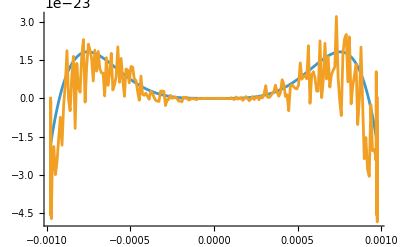

```mathematica
Plot[{sin0ExactRelativeError[x],sin0IEEERelativeError[x]},{x,min,max},WorkingPrecision->30,PlotPoints->200,PlotRange->Full]
```

```mathematica
sin0RoundedCoefficients=Map[CorrectlyRound,CoefficientList[sin0Approximation[x],x]]
```

{0,0,0,-6004799503160661/36028797018963968,0,2401919752500293/288230376151711744}

```mathematica
s3=sin0RoundedCoefficients[[4]];
```

```mathematica
HexLiteral[s3,Quotes->4]
```

-0x1.5555'5555'5555'5p-3

```mathematica
s5=sin0RoundedCoefficients[[6]];
```

```mathematica
HexLiteral[s5,Quotes->4]
```

0x1.1111'10B4'0E88'Ap-7

```mathematica
End[]
```

PolynomialSinNearZero`

### Sin Between Table Entries

We we use the sinFn function with an error function suitable for the absolute error.

```mathematica
cosApproximation;
cosApproximationResult;
sinApproximation;
sinApproximationResult;
xInterval;
```

```mathematica
Begin["PolynomialSinBetweenTableEntries`"]
```

PolynomialSinBetweenTableEntries`

Build a symmetrical interval, because our polynomial is going to be odd anyway:

```mathematica
max=Max[ub,-lb];
```

```mathematica
min=-max;
```

```mathematica
xInterval=Interval[{min,max}];
```

```mathematica
N[Log2[max-1/1024]]
```

-17.8343

```mathematica
sinApproximationResult=GeneralMiniMaxApproximation[
{t^2,If[t==0,-1/6,sinFn[t]],If[t==0,1,1/t^3]},
{t,{0,max},1,0},
x,WorkingPrecision->30]
```

{{0,0.000791244789622416524109556573954,0.00098084145953036827592086410732},{-0.166666666666666666666666651257+0.00833333315942546934238072142829 x,-1.54101011444748050381637877789×10^-26}}

```mathematica
sinApproximation=Function[u, Evaluate[ u^3 (sinApproximationResult[[2,1]]/.x->u^2)]]
```

Function[u,u^3 (-0.166666666666666666666666651257+0.00833333315942546934238072142829 u^2)]

```mathematica
sinExactAbsoluteError = Function[u,u+ sinApproximation[u]-Sin[u]]
```

Function[u,u+sinApproximation[u]-Sin[u]]

```mathematica
sinIEEEAbsoluteError = Function[u,u+IEEEEvaluate[ sinApproximation[u]]-Sin[u]]
```

Function[u,u+IEEEEvaluate[sinApproximation[u]]-Sin[u]]

The plot of the absolute error with floating-point evaluation is noisy:

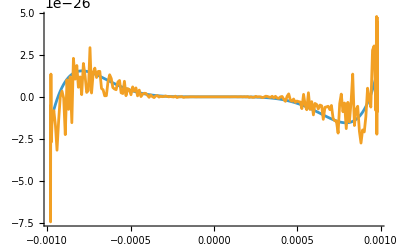

```mathematica
Plot[{sinExactAbsoluteError[x],sinIEEEAbsoluteError[x]},{x,min,max},WorkingPrecision->30,PlotPoints->200,PlotRange->Full]
```

```mathematica
sinRoundedCoefficients=Map[CorrectlyRound,CoefficientList[sinApproximation[x],x]]
```

{0,0,0,-6004799503160661/36028797018963968,0,4803839502277471/576460752303423488}

```mathematica
s3=sinRoundedCoefficients[[4]];
```

```mathematica
HexLiteral[s3,Quotes->4]
```

-0x1.5555'5555'5555'5p-3

```mathematica
s5=sinRoundedCoefficients[[6]];
```

```mathematica
HexLiteral[s5,Quotes->4]
```

0x1.1111'10B1'75B5'Fp-7

```mathematica
End[]
```

PolynomialSinBetweenTableEntries`

### Cos Between Table Entries

We use the cosFn function with an error function suitable for the absolute error.

```mathematica
Begin["PolynomialCosBetweenTableEntries`"]
```

PolynomialCosBetweenTableEntries`

Build a symmetrical interval, because our polynomial is going to be even anyway:

```mathematica
max=Max[ub,-lb];
```

```mathematica
min=-max;
```

```mathematica
xInterval=Interval[{min,max}];
```

```mathematica
cosApproximationResult=GeneralMiniMaxApproximation[
{t^2,If[t==0,-1/2,cosFn[t]],If[t==0,1,1/t^2]},
{t,{0,max},1,0},
x,WorkingPrecision->30]
```

{{0,0.000757265291358836985640765784057,0.00098084145953036827592086410732},{-0.499999999999999999999869043914+0.0416666654719775656776131245243 x,-1.30956085548072217208059971157×10^-22}}

```mathematica
cosApproximation=Function[u, Evaluate[ u^2 (cosApproximationResult[[2,1]]/.x->u^2)]]
```

Function[u,u^2 (-0.499999999999999999999869043914+0.0416666654719775656776131245243 u^2)]

```mathematica
cosExactAbsoluteError = Function[u,1+ cosApproximation[u]-Cos[u]]
```

Function[u,1+cosApproximation[u]-Cos[u]]

```mathematica
cosIEEEAbsoluteError = Function[u,1+IEEEEvaluate[ cosApproximation[u]]-Cos[u]]
```

Function[u,1+IEEEEvaluate[cosApproximation[u]]-Cos[u]]

The plot of the absolute error with floating-point evaluation is noisy:

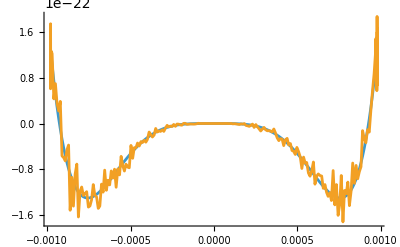

```mathematica
Plot[{cosExactAbsoluteError[x],cosIEEEAbsoluteError[x]},{x,min,max},WorkingPrecision->30,PlotPoints->200,PlotRange->Full]
```

```mathematica
cosRoundedCoefficients=Map[CorrectlyRound,CoefficientList[cosApproximation[x],x]]
```

{0,0,-1/2,0,6004799330987817/144115188075855872}

Note that the fact that this coefficient is a power of two has no effect on the accuracy as it’s used as part of an FMA.

```mathematica
c2=cosRoundedCoefficients[[3]];
```

```mathematica
HexLiteral[c2,Quotes->4]
```

-0x1.0000'0000'0000'0p-1

```mathematica
c4=cosRoundedCoefficients[[5]];
```

```mathematica
HexLiteral[c4,Quotes->4]
```

0x1.5555'54B1'22F2'9p-5

Error on the minimax approximation:

```mathematica
End[]
```

PolynomialCosBetweenTableEntries`

## Error Analysis

```mathematica
Options[mullerE]={UseFMA->False};
mullerE[ϵ1_Real,OptionsPattern[]]:=Module[{k=Floor[-Log2[ϵ1]-M],e},Assert[k>=3];e=If[OptionValue[UseFMA],1,(1-2^-M)^-1](1+2^(M+1) ϵ1/(1-ϵ1-2^(-k+1)));Assert[e<=2];e]
```

### Sin Near Zero

```mathematica
Begin["ErrorSinNearZero`"]
```

ErrorSinNearZero`

```mathematica
max=Max[x0Interval]
```

1/1024

Error on the minimax approximation:

```mathematica
η=Abs[sin0ApproximationResult[[2,2]]]
```

1.82236374808329308166866751883×10^-23

```mathematica
Log2[η]
```

-75.5385352292084490035624057487

Error due to the floating-point evaluation:

This analysis  will need to be documented !

```mathematica
sin0ApproximationIEEEIntervals=IEEEEvaluateWithRelativeError[sin0Approximation[x0Interval]]
```

{Interval[{-6004799503160661/38685626227668133590597632,6004799503160661/38685626227668133590597632}],Interval[{-4.9960027370375×10^-16,3.8857817776014×10^-16}]}

```mathematica
δ1=Interval[{-η,η}]
```

Interval[{-1.82236374808329308166866751883×10^-23,1.82236374808329308166866751883×10^-23}]

```mathematica
δ2=sin0ApproximationIEEEIntervals[[2]]
```

Interval[{-4.9960027370375×10^-16,3.8857817776014×10^-16}]

```mathematica
δ3=uInterval
```

Interval[{-1/9007199254740992,1/9007199254740992}]

```mathematica
sin0ImplementationRelativeError[x_,e_]:=(x+(((1-δ1)Sin[x]-x)(1+δ2)+e)(1+δ3))/Sin[x+e]-1
```

The relative error is monotonic over the domain of interest:

```mathematica
Plot3D[{Min[sin0ImplementationRelativeError[x,e]],Max[sin0ImplementationRelativeError[x,e]]},{x,0,max},{e,-max 𝔲[1/2],max 𝔲[1/2]},RegionFunction->Function[{x,e},-x 𝔲[1/2]<e<x 𝔲[1/2]],WorkingPrecision->40,MeshShading->{{Automatic,None},{None,Automatic}},PlotStyle->{Red,Blue}]
```

-Graphics3D-

```mathematica
smol=1*^-100;
```

```mathematica
corners={{smol,-smol 𝔲[1/2]},{smol,smol 𝔲[1/2]},{max,-max 𝔲[1/2]},{max,max 𝔲[1/2]}};
```

```mathematica
relativeErrorsAtCorners=Map[Apply[sin0ImplementationRelativeError,#]&,corners]
```

{Interval[{-1.8223637493158893588533215209×10^-23,1.822363749315888954207283048×10^-23}],Interval[{-1.8223637493158885495612443015×10^-23,1.8223637493158889542072827743×10^-23}],Interval[{-1.5057256748115×10^-22,6.2339929532401×10^-23}],Interval[{-4.4693440635197×10^-23,1.68219056329054×10^-22}]}

```mathematica
sin0ImplementationMaxRelativeError=Max[Abs/@relativeErrorsAtCorners]
```

1.68219056329054×10^-22

```mathematica
Log2[sin0ImplementationMaxRelativeError]
```

-72.33207694010874

This error preserves 19 bits after the mantissa of the result, which is sufficient for ensuring correct rounding with high probability.

Rounding test:

```mathematica
e=mullerE[sin0ImplementationMaxRelativeError,UseFMA->True]
```

1.0000030303766775702

```mathematica
HexLiteral[CorrectlyRound[e,RoundingMode->TowardPositiveInfinity],Quotes->4]
```

0x1.0000'32D7'5E64'Cp0

Proof that the term in e x^2 doesn’t matter:

```mathematica
Collect[Normal[Series[Sin[u],{u,0,5}]]/.u->(x+e),e]/.(e^n_:>0/;n>=2)
```

1.0000030303766775702+x-1/6 (1.0000030303766775702+x)^3+1/120 (1.0000030303766775702+x)^5

```mathematica
𝔲[1/2] max^2/2//Log2
```

-74

```mathematica
End[]
```

ErrorSinNearZero`

### Between Table Entries

These analyses  will need to be documented !

Error on the minimax approximations:

```mathematica
ηs=Abs[sinApproximationResult[[2,2]]]
```

1.54101011444748050381637877789×10^-26

```mathematica
ηc=Abs[cosApproximationResult[[2,2]]]
```

1.30956085548072217208059971157×10^-22

```mathematica
Log2[{ηs,ηc}]
```

{-85.74625413603291245476729447003,-72.6933349840302756413104541058}

```mathematica
δ1=Interval[{-ηs,ηs}];
```

```mathematica
δ2=Interval[{-ηc,ηc}];
```

Error due to the floating-point evaluation:

```mathematica
sinApproximationIEEEIntervals=IEEEEvaluateWithAbsoluteError[sinApproximation[xInterval]]
```

{Interval[{-3042039368118061/19342813113834066795298816,3042039368118061/19342813113834066795298816}],Interval[{-6.9291627640173×10^-26,6.9291627640173×10^-26}]}

```mathematica
cosApproximationIEEEIntervals=IEEEEvaluateWithAbsoluteError[cosApproximation[xInterval]]
```

{Interval[{-4543152527193641/9444732965739290427392,0}],Interval[{-1.325814992905×10^-22,1.3258124826762×10^-22}]}

```mathematica
δ3=sinApproximationIEEEIntervals[[2]]
```

Interval[{-6.9291627640173×10^-26,6.9291627640173×10^-26}]

```mathematica
δ4=cosApproximationIEEEIntervals[[2]]
```

Interval[{-1.325814992905×10^-22,1.3258124826762×10^-22}]

#### Sin

```mathematica
Begin["ErrorSinBetweenTableEntries`"]
```

ErrorSinBetweenTableEntries`

```mathematica
δ5=uInterval;
```

```mathematica
δ6=uInterval;
```

```mathematica
δ7=uInterval;
```

```mathematica
δ8=uInterval;
```

```mathematica
ϵ=uInterval;
```

```mathematica
(*δ1=.;δ2=.;δ3=.;δ4=.;δ5=.;δ6=.;δ7=.;δ8=.;*)
```

```mathematica
qs[h_]:=Sin[h]-h-δ1+δ3
```

```mathematica
qc[h_]:=Cos[h]-1-δ2+δ4
```

```mathematica
t[h_,s0_,c0_]:=c0 h + s0
```

```mathematica
u[h_,s0_]:=s0  qc[h](1+δ5)
```

```mathematica
v[h_,s0_,c0_]:=(c0 qs[h]+u[h,s0])(1+δ6)
```

```mathematica
s[h_,e_,s0_,c0_]:=t[h,s0,c0](1+ϵ((1+δ7)(1+δ8)-1))+(v[h,s0,c0]+c0 e (1+δ7))(1+δ8)
```

```mathematica
sinImplementationRelativeError[h_,e_,x0_,s0_,c0_]:=s[h,e,s0,c0]/Sin[x0+h+e]-1
```

```mathematica
m=Max[Abs[accurateTablesIntervals[[3]]]]
```

281475950594527/288230376151711744

```mathematica
at=accurateTables[3]
```

{1688850834147807/288230376151711744,140303435264035439681048965270098829287830998095831/23945242826029513411849172299223580994042798784118784,93534499138265492608207770591518797753179840250735/93536104789177786765035829293842113257979682750464}

```mathematica
Plot3D[{Min[sinImplementationRelativeError[h,e,at[[1]],at[[2]],at[[3]]]],Max[sinImplementationRelativeError[h,e,at[[1]],at[[2]],at[[3]]]]},{h,0,m},{e,-m 𝔲[1/2],m 𝔲[1/2]},WorkingPrecision->30,MeshShading->{{Automatic,None},{None,Automatic}},PlotStyle->{Red,Blue}]
```

-Graphics3D-

```mathematica
sinImplementationMaxRelativeErrorPerInterval[i_]:=Module[
{at=accurateTables[i],m=Max[Abs[accurateTablesIntervals[[i]]]],aec,corners},
corners={{0,-m 𝔲[1/2]},{0,m 𝔲[1/2]},{m,-m 𝔲[1/2]},{m,m 𝔲[1/2]}};
aec=Map[sinImplementationRelativeError[#[[1]],#[[2]],at[[1]],at[[2]],at[[3]]]&,corners];
Max[Abs/@aec]
]
```

```mathematica
sinImplementationMaxRelativeError=Max[Table[sinImplementationMaxRelativeErrorPerInterval[i],{i,1,accurateTablesMaxIndex}]];
```

```mathematica
Log2[sinImplementationMaxRelativeError]
```

-70.67597488504957

Rounding test:

```mathematica
e=mullerE[sinImplementationMaxRelativeError,UseFMA->True];
```

```mathematica
HexLiteral[CorrectlyRound[e,RoundingMode->TowardPositiveInfinity],Quotes->4]
```

0x1.0000'A03C'34D3'9p0

```mathematica
End[]
```

ErrorSinBetweenTableEntries`

#### Cos

```mathematica
Begin["ErrorsCosBetweenTableEntries`"]
```

ErrorsCosBetweenTableEntries`

```mathematica
δ5=uInterval;
```

```mathematica
δ6=uInterval;
```

```mathematica
δ7=uInterval;
```

```mathematica
δ8=uInterval;
```

```mathematica
ϵ=uInterval;
```

```mathematica
(*δ1=.;δ2=.;δ3=.;δ4=.;δ5=.;δ6=.;δ7=.;δ8=.;*)
```

```mathematica
qs[h_]:=Sin[h]-h-δ1+δ3
```

```mathematica
qc[h_]:=Cos[h]-1-δ2+δ4
```

```mathematica
t[h_,s0_,c0_]:=c0 -h s0
```

```mathematica
u[h_,c0_]:=c0  qc[h](1+δ5)
```

```mathematica
v[h_,s0_,c0_]:=(-s0 qs[h]+u[h,c0])(1+δ6)
```

```mathematica
c[h_,e_,s0_,c0_]:=t[h,s0,c0](1+ϵ((1+δ7)(1+δ8)-1))+(v[h,s0,c0]-s0 e (1+δ7))(1+δ8)
```

```mathematica
cosImplementationRelativeError[h_,e_,x0_,s0_,c0_]:=c[h,e,s0,c0]/Cos[x0+h+e]-1
```

```mathematica
m=Max[Abs[accurateTablesIntervals[[3]]]]
```

281475950594527/288230376151711744

```mathematica
at=accurateTables[3]
```

{1688850834147807/288230376151711744,140303435264035439681048965270098829287830998095831/23945242826029513411849172299223580994042798784118784,93534499138265492608207770591518797753179840250735/93536104789177786765035829293842113257979682750464}

```mathematica
Plot3D[{Min[cosImplementationRelativeError[h,e,at[[1]],at[[2]],at[[3]]]],Max[cosImplementationRelativeError[h,e,at[[1]],at[[2]],at[[3]]]]},{h,-m,m},{e,-m 𝔲[1/2],m 𝔲[1/2]},WorkingPrecision->30,MeshShading->{{Automatic,None},{None,Automatic}},PlotStyle->{Red,Blue}]
```

-Graphics3D-

```mathematica
cosImplementationRelativeError[m/2,m 𝔲[1/2],at[[1]],at[[2]],at[[3]]]//N
```

Interval[{-2.50304×10^-22,3.56184×10^-22}]

```mathematica
cosImplementationMaxRelativeErrorPerInterval[i_]:=Module[
{at=accurateTables[i],m=Max[Abs[accurateTablesIntervals[[i]]]],aec,corners},
corners={{0,-m 𝔲[1/2]},{0,m 𝔲[1/2]},{m,-m 𝔲[1/2]},{m,m 𝔲[1/2]}};
aec=Map[cosImplementationRelativeError[#[[1]],#[[2]],at[[1]],at[[2]],at[[3]]]&,corners];
Max[Abs/@aec]
]
```

```mathematica
cosImplementationMaxRelativeError=Max[Table[cosImplementationMaxRelativeErrorPerInterval[i],{i,1,accurateTablesMaxIndex}]];
```

```mathematica
Log2[cosImplementationMaxRelativeError]
```

-70.67365925522692

Rounding test:

```mathematica
e=mullerE[cosImplementationMaxRelativeError,UseFMA->True];
```

```mathematica
HexLiteral[CorrectlyRound[e,RoundingMode->TowardPositiveInfinity],Quotes->4]
```

0x1.0000'A07E'1980'8p0

```mathematica
End[]
```

ErrorsCosBetweenTableEntries`